If[x≥0,x,0]

0.05

0.05

0.05

«1 more identical outputs»

0.801589+0.584869 If[-1.18991+1.45555 x1-1.47735 x2≥0,-1.18991+1.45555 x1-1.47735 x2,0]-0.278228 If[-0.698776+0.745913 x1-0.767524 x2≥0,-0.698776+0.745913 x1-0.767524 x2,0]+0.287501 If[-0.0798414-0.746532 x1-0.705037 x2≥0,-0.0798414-0.746532 x1-0.705037 x2,0]-0.576385 If[-0.0415539-0.0194702 x1-0.591337 x2≥0,-0.0415539-0.0194702 x1-0.591337 x2,0]-0.766154 If[-1.00726+0.2395 x1-0.437476 x2≥0,-1.00726+0.2395 x1-0.437476 x2,0]-0.556941 If[-0.283958+0.144197 x1-0.153565 x2≥0,-0.283958+0.144197 x1-0.153565 x2,0]-1.21432 If[-0.0345868-0.630031 x1-0.104419 x2≥0,-0.0345868-0.630031 x1-0.104419 x2,0]+0.0469487 If[0.0885937-0.19396 x1-0.0833692 x2≥0,0.0885937-0.19396 x1-0.0833692 x2,0]+0.301957 If[0.637901-0.00727679 x1-0.0475682 x2≥0,0.637901-0.00727679 x1-0.0475682 x2,0]-0.393783 If[-0.136188-0.0477271 x1-0.0333902 x2≥0,-0.136188-0.0477271 x1-0.0333902 x2,0]-0.323058 If[0.286011-0.160687 x1+0.00654517 x2≥0,0.286011-0.160687 x1+0.00654517 x2,0]-0.568001 If[-0.00279802-0.0250004 x1+0.0123498 x2≥0,-0.00279802-0.0250004 x1+0.0123498 x2,0]+0.0667024 If[-0.647812+0.102419 x1+0.247487 x2≥0,-0.647812+0.102419 x1+0.247487 x2,0]-0.551786 If[-1.3166-0.413454 x1+0.261295 x2≥0,-1.3166-0.413454 x1+0.261295 x2,0]-0.20762 If[0.483624-0.320353 x1+0.345099 x2≥0,0.483624-0.320353 x1+0.345099 x2,0]+0.653168 If[-0.909159-1.37587 x1+1.32657 x2≥0,-0.909159-1.37587 x1+1.32657 x2,0]

-0.0388924

-0.0388924

-0.0484744+0.943632 If[-0.0681402-0.473692 x1-2.03285 x2≥0,-0.0681402-0.473692 x1-2.03285 x2,0]+0.359518 If[-0.109205-1.50412 x1-1.23453 x2≥0,-0.109205-1.50412 x1-1.23453 x2,0]-0.543925 If[-0.14715-0.216056 x1-0.813417 x2≥0,-0.14715-0.216056 x1-0.813417 x2,0]+0.0056868 If[-0.353551+0.0838769 x1-0.555892 x2≥0,-0.353551+0.0838769 x1-0.555892 x2,0]+0.00093025 If[0.427792-0.79669 x1-0.549537 x2≥0,0.427792-0.79669 x1-0.549537 x2,0]+0.0618424 If[0.0238133-0.000995222 x1-0.0596628 x2≥0,0.0238133-0.000995222 x1-0.0596628 x2,0]+0.0544212 If[-1.15486+0.323469 x1-0.00593725 x2≥0,-1.15486+0.323469 x1-0.00593725 x2,0]+0.00455504 If[-0.488826-0.981627 x1+0.101747 x2≥0,-0.488826-0.981627 x1+0.101747 x2,0]

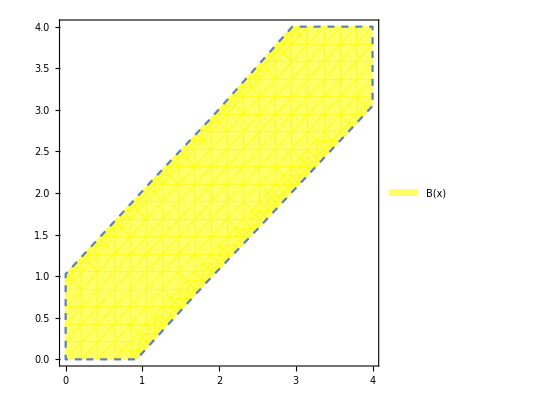

print[g_b]

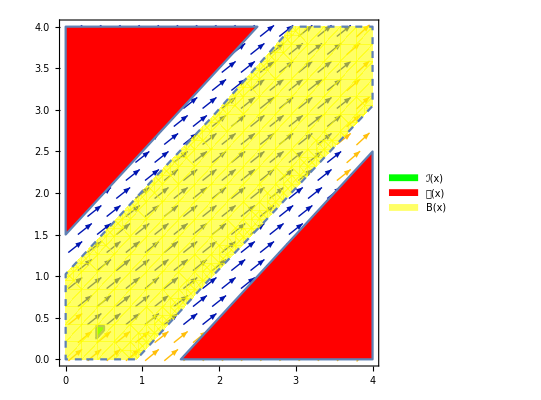

-Graphics-

```mathematica
(*phi=RegionPlot[(x≥0&&x≤0.7&&y≥0.7&&y≤1.5&&y-x<=0.8),{x,0,0.7},{y,0.7,1.5},PlotPoints->50,BoundaryStyle->Directive[RGBColor[0,0.5,0], Thin],PlotStyle->Directive[Blue]]
(*phi ->initial region *)
psi1=RegionPlot[(x≥0&&x≤8&&y≥0&&y≤8&&(y-x)*(y-x)>=1),{x,0,8},{y,0,8},PlotPoints->70,PlotStyle->Directive[Red],BoundaryStyle->Directive[RGBColor[0.5,0,0], Opacity[0.05],Thin]]*)
(* we first give ReLU fuction*)
relu[x_] =If[x>=0,x,0]
(*psi -> unsafe region*)

(*B(x,xˆ)=0.9227x1*x1+0.2348v1*v1+0.9227x2*x2+0.2348v2*v2+0.006x1*v1−0.006x2*v1−0.006x1*v2−0.006x2*v2−0.4696v1*v2−1.845x1x2−0.0002*x2+0.0728,*)
(* this B is only for test*)
(*bc=0.9227*x*x + 0.9227*y*y -1.845*x*y  - 0.0002*y + 0.0728*)
x3 =0.05
x4 =0.05
x5 = 0.05
x6 =0.05

bc =0.653168383819071*relu[-1.37587249602747*x1+1.3265679322654*x2+1.21051567105589*x3-0.566539193773866*x4+0.596966164432249*x5+1.90032689114056*x6-1.06622206323476]+0.287500659318123*relu[-0.746532331180631*x1-0.705037425074263*x2-0.237705337686504*x3+0.310295008848059*x4-0.583971252605835*x5-0.347783041308123*x6-0.0368832187381405]-1.21431809232748*relu[-0.630031228076897*x1-0.104419237218942*x2+0.321790567033104*x3+0.119533985395514*x4-0.151509984351134*x5+0.610286668207226*x6-0.0795918535297378]-0.551785926804486*relu[-0.413453688490663*x1+0.261295060362235*x2-0.258598457447132*x3+0.572048743060896*x4-0.831731389841352*x5+0.151117474600796*x6-1.29824077076795]-0.207620263146355*relu[-0.320352942511297*x1+0.345099475196438*x2+0.243937577028745*x3-0.275486918022506*x4-0.618234628929868*x5-0.368265316450336*x6+0.534526663657799]+0.0469487020929378*relu[-0.193960310338403*x1-0.0833691716484224*x2-0.305932895326386*x3+0.493419574997604*x4+1.5442606478614*x5+0.923906949276937*x6-0.0441889679138864]-0.323057572283815*relu[-0.160686511738106*x1+0.00654516643657638*x2-0.966695342443601*x3+0.0754629289920884*x4-0.226728152326308*x5-0.84214275403355*x6+0.384015967707447]-0.393782835651562*relu[-0.0477270505123467*x1-0.033390160864476*x2-0.175166031377548*x3-1.4915487746246*x4-1.37112799036526*x5-0.878492007849963*x6+0.0596288481492746]-0.568000664325029*relu[-0.0250003563790281*x1+0.0123497760082222*x2+0.457923022169683*x3-1.74116571681844*x4-1.81392689527461*x5-1.3309793495275*x6+0.218609423499953]-0.576385499028512*relu[-0.0194701630727383*x1-0.591336777619429*x2-0.05432233855495*x3+0.137324740610351*x4-0.181740736954558*x5-0.448431829668436*x6-0.0141953616249391]+0.301957007550712*relu[-0.00727679066026686*x1-0.0475682019600544*x2+0.00359437989159234*x3+1.33100274846629*x4+0.332916353695399*x5+0.790248051626644*x6+0.515012787468363]+0.0667024303414686*relu[0.102418835938383*x1+0.247487046071189*x2+0.0877335509192933*x3+0.295369369299974*x4+0.459490431071939*x5+0.865565370910817*x6-0.733220056559543]-0.556941130608669*relu[0.144196645439096*x1-0.153564527786211*x2+1.02855128330188*x3-1.64425176063248*x4-1.28371688176382*x5-0.967448547264865*x6-0.140614723773022]-0.766153540114888*relu[0.239499523150767*x1-0.437476008786239*x2-0.325114238285051*x3+0.142158500581772*x4-0.170517481843829*x5-0.339715113374142*x6-0.972598574661303]-0.278227787449064*relu[0.745913080478928*x1-0.767523947228908*x2-0.819554515510669*x3-0.498424370219287*x4-0.0663049386869918*x5-0.0715380039027626*x6-0.625984610730391]+0.584869275458593*relu[1.4555537289475*x1-1.47734879770534*x2-1.49091970488976*x3+0.970313951325498*x4+1.26199677789449*x5-0.0360401617062209*x6-1.22517573195205]+0.801589009740621

(*uˆ(x,ˆx,u)=0.8x1−0.8x2+1.5ˆx1−1.5ˆx2+u.*)
(*this is controller*)

(* xuebai *)
initialPlot=RegionPlot[(x1≥0.4&&x1≤0.5&&x2≥0.25&&x2≤0.4&&x1-x2<=0.15),{x1,0.4,0.5},{x2,0.25,0.4},PlotStyle->Directive[Green],PlotLegends->SwatchLegend[{"ℐ(x)"}]];
unsafePlot=RegionPlot[(x1≥0&&x1≤4&&x2≥0&&x2≤4&&(x2-x1)*(x2-x1)>=1.5*1.5),{x1,0,4},{x2,0,4},PlotStyle->Directive[Red],PlotLegends->SwatchLegend[{"𝒰(x)"}]];
bcPlot=RegionPlot[(x1≥0&&x1≤4&&x2≥0&&x2≤4&&bc<=1),{x1,0,4},{x2,0,4},BoundaryStyle->{Dashed},PlotStyle->Directive[Opacity[.6],Yellow],PlotLegends->SwatchLegend[{"B(x)"}]];
u = Random[Real,{-0.05,-0.03}]
x7 = u

uhat = 0.359518099730174*relu[-1.50412051664786*x1-1.23452631878726*x2+0.160110977019438*x3-0.825780841104468*x4-1.86172712560357*x5+0.537532916130876*x6-0.395709065360913*x7-0.0251016463121472]+0.00455504021811348*relu[-0.981627420148361*x1+0.101747365095651*x2-0.728417048167582*x3+2.13364536776983*x4-0.698972800017011*x5+0.959366238334601*x6+2.18644171384934*x7-0.487070998005881]+0.000930249757553318*relu[-0.796689964410922*x1-0.549537271708421*x2+0.0502492258204252*x3-1.21181261273066*x4-0.572588222039728*x5-1.93137283312484*x6+0.235533152320751*x7+0.620228166936427]+0.943632237540789*relu[-0.473692469223066*x1-2.03284560264282*x2+0.490971618808139*x3-0.215890415916864*x4+0.194715691160504*x5-0.720894606678345*x6+0.296294943780714*x7-0.0440617471951797]-0.543924638785298*relu[-0.216056162447391*x1-0.813416521235552*x2+0.815707432769874*x3+0.0875140020138602*x4+0.227688378691275*x5+1.90670127867011*x6-0.493259570631074*x7-0.318214955499413]+0.0618424484619708*relu[-0.000995221645980706*x1-0.0596628347593902*x2-0.0869631182249101*x3+0.173432919360962*x4+1.34212191565388*x5-1.59720362935724*x6-0.569338841341844*x7+0.0101009272672619]+0.00568679970114664*relu[0.0838768662717042*x1-0.555892391066658*x2-2.00852457873965*x3-0.315317071091857*x4+0.436729502666019*x5-1.08613670301085*x6+0.939626784730386*x7-0.168344170802611]+0.0544212166820255*relu[0.323469472102739*x1-0.00593725049057356*x2-1.01940408750193*x3+1.1225878576842*x4-1.12356626445259*x5+0.898185792428886*x6-2.21103890944168*x7-1.23474489553437]-0.0484744354063131
flowPlot=VectorPlot[{0.5*x3 + x5+u,0.5*x4+x6+uhat},{x1,0,4},{x2,0,4},VectorStyle->{Arrowheads[0.03],blue}];

g_b = Show[bcPlot]
print[g_b]

graphics=Show[flowPlot,initialPlot,unsafePlot,bcPlot]
Print[graphics];
```

```mathematica
|
```